0.552384

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

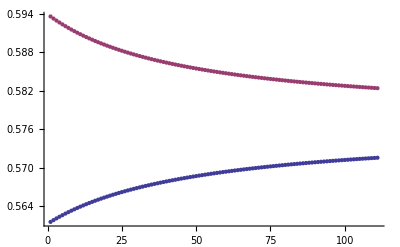

listY

```mathematica
(* Clear all data before calculations *)
Clear[x, r12, r21, r34, r43, z, r13, r31, r24, r42, diag, r14, r41, r23, r32, clight, ωp, fp, γ, sol, M];

(* Length of nanorods *)
x = 100;
r12 = x;
r21 = x;
r34 = x;
r43 = x;

(* Distance btw nanorods *)
z = 30;
r13 = z;
r31 = z;
r24 = z;
r42 = z;

(* Diagonal distance btw dipoles *)
diag = Sqrt[x^2 + z^2];
r14 = diag;
r41 = diag;
r23 = diag;
r32 = diag;

(* Constants *)
clight = 1;
γ = 0.01;
ωp = 1;
a = 2;


(* Drude model & phys functions *)
ϵ[ω_] := 1- ωp^2/(ω^2+ ⅈ γ ω);
α[ω_] := (ϵ[ω] - 1)/(ϵ[ω]+2) a^3; 
k[ω_] :=ω/clight ;

(* Define tensor components *)

χ12[ω_] := 1 /r12 * (-2 ⅈ k[ω] /r12 + 2/r12); (* Parallel Ox *)
χ13[ω_] := 1 /r13 * (k[ω]^2 + ⅈ k[ω] /r13 - 1/r13^2); (* Parallel Oz *)
χ14[ω_] :=  1  (1/r14 * (k[ω]^2 + ⅈ k[ω] /r14 - 1/r14^2) - x^2/r14^3 (k[ω]^2 + ⅈ 3 k[ω] /r14  -3/r14^2));(* Diagonal Ox, Oz *)

χ21[ω_] := 1 /r21 * (-2 ⅈ k[ω] /r21 + 2/r21);(* Parallel Ox *)
χ23[ω_] := 1  (1/r23 * (k[ω]^2 + ⅈ k[ω]/r23 - 1/r23^2) - x^2/r23^3 (k[ω]^2 + ⅈ 3 k[ω] /r23  -3/r23^2));
(* Diagonal Ox, Oz *)
χ24[ω_] := 1 /r24 * (k[ω]^2 + ⅈ k[ω] /r24 - 1/r24^2); (* Parallel Oz *)

χ31[ω_] := 1 /r31 * (k[ω]^2 + ⅈ k[ω] /r31 - 1/r31^2); (* Parallel Oz *)
χ32[ω_] := 1  (1/r32 * (k[ω]^2 + ⅈ k[ω] /r32 - 1/r32^2) - x^2/r32^3 (k[ω]^2 + ⅈ 3 k[ω] /r32  -3/r32^2));
(* Diagonal Ox, Oz *)
χ34[ω_] := 1 /r34 * (-2 ⅈ k[ω] /r34 + 2/r34); (* Parallel Ox *)

χ41[ω_] := 1  (1/r41 * (k[ω]^2 + ⅈ k[ω] /r41 - 1/r41^2) - x^2/r41^3 (k[ω]^2 + ⅈ 3 k[ω] /r41  -3/r41^2));
(* Diagonal Ox, Oz *)
χ42[ω_] := 1 /r42 * (k[ω]^2 + ⅈ k[ω] /r42 - 1/r42^2); (* Parallel Oz *)
χ43[ω_] := 1 /r43 * (-2 ⅈ k[ω] /r43 + 2/r43); (* Parallel Ox *)

(* Creating matrix and finding resonance frequencies *)
M = {{-1/α[ω], χ12[ω], χ13[ω], χ14[ω]}, {χ21[ω], -1/α[ω], χ23[ω], χ24[ω]}, {χ31[ω], χ32[ω], -1/α[ω], χ34[ω]}, {χ41[ω], χ42[ω], χ43[ω], -1/α[ω]}};
sol = FindRoot[Det[M]==0, {ω, 0.01}][[1]][[2]];
w = Abs[sol]
Re[sol];

Clear[ω, sol1, sol2, w, z, listY1, listY2, listY, listX];
listX = {};
listY1 = {};
listY2 = {};
Do[z = i;
r13 = z;
r31 = z;
r24 = z;
r42 = z;
AppendTo[listX, N[z]];
M = {{-1/α[ω], χ12[ω], χ13[ω], χ14[ω]}, {χ21[ω], -1/α[ω], χ23[ω], χ24[ω]}, {χ31[ω], χ32[ω], -1/α[ω], χ34[ω]}, {χ41[ω], χ42[ω], χ43[ω], -1/α[ω]}};
sol1 = FindRoot[Det[M]==0, {ω, 0.55}][[1]][[2]];
w = Abs[sol1];
AppendTo[listY1, w];
sol2 = FindRoot[Det[M]==0, {ω, 0.6}][[1]][[2]];
w = Abs[sol2];
AppendTo[listY2, w], {i, 50, 160, 1}]
ListPlot[{listY1, listY2}]
listY
```